## Images

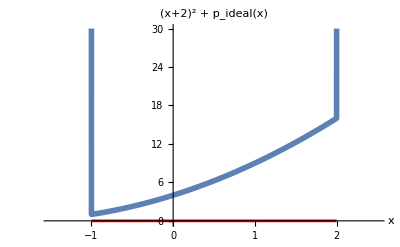

```mathematica
Show[Plot[If[x≥-1 &&x≤2,(x+2)^2,100],{x,-1.5,2.5},PlotStyle->Thickness[.01],AxesLabel->{"x",""},PlotRange->{-.2,30},PlotLabel->"(x+2)^2 + p_ideal(x)"],Graphics[{Thickness[.005],Red,Line[{{-1,0},{2,0}}]}]]
```

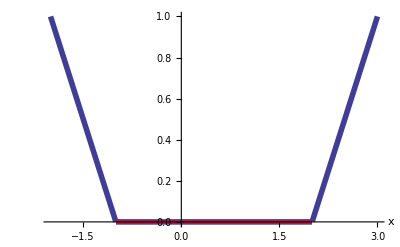

```mathematica
Show[Plot[-Min[{(x+1),0}]-Min[{(2-x),0}],{x,-2,3},PlotStyle->Thickness[.01],AxesLabel->{"x",""}],Graphics[{Thickness[.005],Red,Line[{{-1,0},{2,0}}]}]]
```

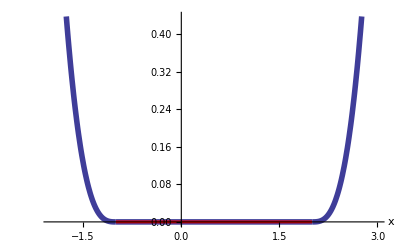

```mathematica
Show[Plot[-Min[{(x+1),0}]^3-Min[{(2-x),0}]^3,{x,-2,3},PlotStyle->Thickness[.01],AxesLabel->{"x",""}],Graphics[{Thickness[.005],Red,Line[{{-1,0},{2,0}}]}]]
```

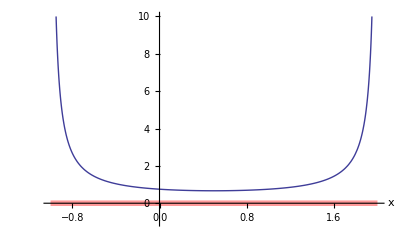

```mathematica
Show[Plot[.5/(x+1)+.5/(2-x),{x,-1,2},PlotRange->{-1,10},PlotStyle->Thick,AxesLabel->{"x", ""}],Graphics[{Thickness[.01],Red,Opacity[.4],Line[{{-1,0},{2,0}}]}]]
```

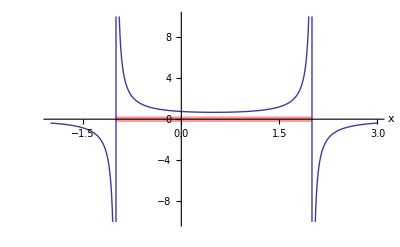

```mathematica
Show[Plot[.5/(x+1)+.5/(2-x),{x,-2,3},PlotRange->{-10,10},PlotStyle->Thick,AxesLabel->{"x", ""}],Graphics[{Thickness[.01],Red,Opacity[.4],Line[{{-1,0},{2,0}}]}]]
```

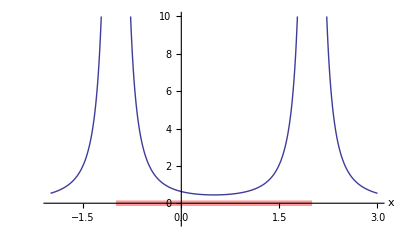

```mathematica
Show[Plot[.5/(x+1)^2+.5/(2-x)^2,{x,-2,3},PlotRange->{-1,10},PlotStyle->Thick,AxesLabel->{"x", ""}],Graphics[{Thickness[.01],Red,Opacity[.4],Line[{{-1,0},{2,0}}]}]]
```

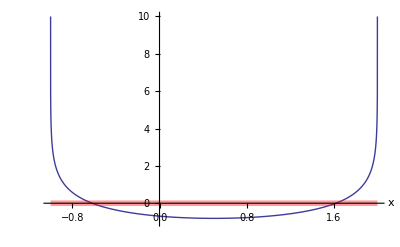

```mathematica
Show[Plot[-Log[(x+1)]-Log[(2-x)],{x,-1,2},PlotRange->{-1,10},PlotStyle->Thick,AxesLabel->{"x", ""}],Graphics[{Thickness[.01],Red,Opacity[.4],Line[{{-1,0},{2,0}}]}]]
```

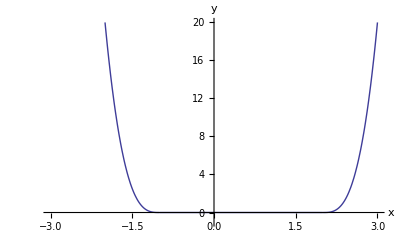

```mathematica
p1=Plot[-20*Min[x+1,0]^3-20*Min[2-x,0]^3,{x,-3,3},PlotRange->{-1,20},PlotStyle->Thick,AxesLabel->{"x", "y"}]
```

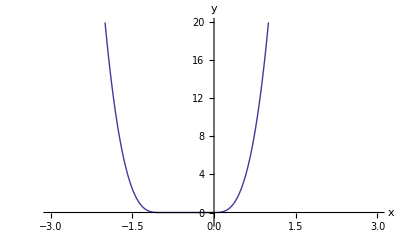

```mathematica
p2=Plot[-20*Min[x+1,0]^3-20*Min[0-x,0]^3,{x,-3,3},PlotRange->{-1,20},PlotStyle->Thick,AxesLabel->{"x", "y"}]
```

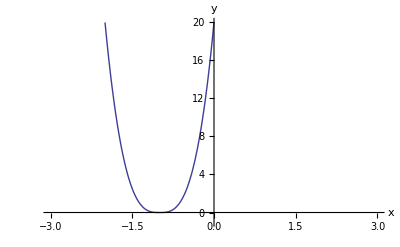

```mathematica
p3=Plot[-20*Min[x+1,0]^3-20*Min[-1-x,0]^3,{x,-3,3},PlotRange->{-1,20},PlotStyle->Thick,AxesLabel->{"x", "y"}]
```

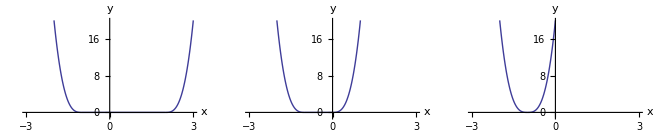

```mathematica
GraphicsGrid[{{p1,p2,p3}}]
```

## Group Problem 1

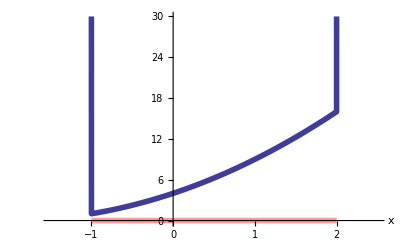

```mathematica
Show[Plot[If[x≥-1 &&x≤2,(x+2)^2,100],{x,-1.5,2.5},PlotStyle->Thickness[.01],AxesLabel->{"x",""},PlotRange->{-.2,30}],Graphics[{Thickness[.01],Red,Opacity[.4],Line[{{-1,0},{2,0}}]}]]
```

## Group Problem 2

```mathematica
Manipulate[Show[Plot[-x/2-λ1*(x+1)-λ2*(2-x),{x,-3,3},PlotRange->{-10,10},PlotStyle->Thick,AxesLabel->{"x", "y"}],Graphics[{PointSize[Large],Red,Point[{2,0}]}],Graphics[{Thickness[.01],Red,Opacity[.4],Line[{{-1,0},{2,0}}]}]],{λ1,0,10},{λ2,0,10}]
```

### penalty only

```mathematica
Manipulate[Show[Plot[-λ1*(x+1)-λ2*(2-x),{x,-3,3},PlotRange->{-10,10},PlotStyle->Thick,AxesLabel->{"x", "y"}],Graphics[{Thickness[.01],Red,Opacity[.4],Line[{{-1,0},{2,0}}]}]],{λ1,0,10},{λ2,0,10}]
```

## Equation Constraints

### inverse barrier

```mathematica
Manipulate[Show[Plot[1/(x+1)+1/(a-x),{x,-3,3},PlotRange->{-1,20},PlotStyle->Thick,AxesLabel->{"x", "y"}],Graphics[{Thickness[.01],Red,Line[{{-1,0},{a,0}}]}]],{{a,2},-1,2}]
```

### log barrier

```mathematica
Manipulate[Show[Plot[0,{x,-3,3},PlotRange->{-1,20},PlotStyle->{Thin,Black}],Plot[-Log[x+1]-Log[a-x],{x,-3,3},PlotRange->{-1,20},PlotStyle->Thick,AxesLabel->{"x", "y"}],Graphics[{Thickness[.01],Red,Line[{{-1,0},{a,0}}]}]],{{a,2},-1,2}]
```

### Cubed min-type penalty

```mathematica
Manipulate[Show[Plot[-20*Min[x+1,0]^3-20*Min[a-x,0]^3,{x,-3,3},PlotRange->{-1,20},PlotStyle->Thick,AxesLabel->{"x", "y"}],Graphics[{Thickness[.005],Red,Line[{{-1,0},{a,0}}]}]],{{a,2},-1,2}]
```

## Lab Exercise

```mathematica
Manipulate[Show[Plot[(x+2)^2+-λ1*Min[x+1,0]^3-λ2*Min[2-x,0]^3,{x,-3,3},PlotRange->{-1,20},PlotStyle->Thick,AxesLabel->{"x", "y"}],Graphics[{PointSize[Large],Red,Point[{-1,0}]}],Graphics[{Thickness[.01],Red,Opacity[.4],Line[{{-1,0},{2,0}}]}]],{λ1,0,1000},{λ2,0,1000}]
```

```mathematica
Manipulate[Minimize[(x+2)^2+-λ1*Min[x+1,0]^3-λ2*Min[2-x,0]^3,x],{λ1,0,1000},{λ2,0,1000}]
```

(a) The penalized minimizer appears to be to the left of -1.
(b) As the value of the constant λ1>0 increases, the penalized minimizer moves closer to the true minimizer at x=-1.